# Visualizing the Bolzano-Weierstrass Theorem

Understanding the convergence of infinite bounded sequences

Lauren Berk, Jun. 26,  2018

Bolzano-Weierstrass is a theorem that seems obvious, until you think about it, and then seems impossible, until you think about it some more.  Proving is another matter entirely.  In this essay, we explore what the theorem says and how to prove it using a visual interpretation of the theorem which is most commonly presented as a very abstract theorem in analysis.

## The idea of convergence

Convergence of functions, convergence of sequences

Those who have taken calculus will be familiar with the idea of “limits” of a function f(x) at a point x_0.  The idea here is, for any value ϵ > 0 you can find a δ > 0 such that, if you restrict your view to the x values around x_0 ( that is, x ∈ (x_0- δ , x_0 + δ)), all of the values of f(x) are within ϵ  of the limit value.  To explore this, you can prove the limit of x*Cos[1/x] at 0 is 0 by dragging the slider to define any ϵ > 0, and getting the necessary δ > 0 in return.  Regardless of what value you set to ϵ, the values of the plot between the vertical lines stay within the corresponding horizontal lines.

```mathematica
Manipulate [Plot[ x*Cos[1/x],{x,-.5,.5},PlotRange->{{-xrange, xrange},{-xrange, xrange}},GridLines->{{-ϵ,ϵ},{- ϵ, ϵ}}],{ϵ,1.*^-7,0.5},{xrange,.0001,.5},SaveDefinitions->True]
```

The idea is the same with sequences (discrete, infinite lists of values).  Here we say a sequence {x_i} converges to a value x_0 if, given any ϵ > 0 you can find a large enough index N so that everything after N in that sequence is within ϵ of x_0.  For example, the sequence: 0, 1/2, 2/3, 3/4, 4/5, ... converges to 1.  Like before, you can use this visualization to specify an ϵ > 0, and an N will be found so that the remainder of the sequence is within ϵ of the limit (1):

```mathematica
Manipulate [ListPlot[Table[n/(n+1),{n,0,3/ϵ}],
PlotRange-> {{0,3/ϵ},{1-2*ϵ, 1+ϵ}},
GridLines->{{1/ϵ,3/ϵ},{1-ϵ,1}}
],{ϵ,.0001,1},SaveDefinitions->True]
```

Of course, just like functions, not all sequences are convergent.  Consider the sequence 1, -1, 1, -1.... no matter how far you go out, you will never be able to find a value smaller than ϵ  = 1 so that all the points are contained around that value.

```mathematica
Manipulate [ListPlot[Table[(-1)^n,{n,0,2*NN}],
PlotRange-> {{0,2*NN},{-2, 2}},
GridLines->{{NN,2*NN},{-1, 1}}
],{NN,1,100},SaveDefinitions->True]
```

Just because a sequence itself doesn’t converge, doesn’t mean we can’t find a *subsequence* that converges.  Using the sequence above (1, -1, 1, -1...) we can select every other number and get a perfectly convergent sequence (1, 1, 1, ....).

On the other hand again, there are some sequences that no matter how hard we try, we cannot find an “infinite handful” of points that converge.  Take the sequence 1, 2, 3, 4.... no matter how clever you are, you cannot pick points from that sequence to form another sequence that “behaves” well.

So when CAN we be sure a sequence will have a convergent subsequence?

## Bolzano-Weierstrass

The Bolzano-Weierstrass theorem states that, if a sequence is bounded, it contains a convergent subsequence. In our examples above, we saw that 1, -1, 1, -1... is bounded, and has a convergent subsequence.  And 1, 2, 3, 4... is not bounded, and does not have a convergent subsequence.  But we cannot extrapolate from these two examples.  We will need to show for ANY bounded sequence, we can find a convergent subsequence.

To make our job more interesting, let’s break out of 1D and think of the problem in 2D.  You can have sequences of pairs, triplets, etc. And Bolzano-Weierstrass should hold for them all.  First let’s visualize  a random sequence in 2D by plotting one point at a time:

```mathematica
pts = RandomReal[{-1,1},{10000,2}];
Manipulate[ListPlot[Take[pts,n],
PlotRange->{{-1,1},{-1,1}}, AspectRatio-> 1],{n,1,1000},SaveDefinitions->True]
```

Since we generated the sequence randomly, we can clearly not say for sure that all the points will be in some narrow range after any point in time.  But, perhaps surprisingly, we can create a rule to color some points (infinitely man) that converge to a point.  This might look something like:

```mathematica
norms = Norm/@({#1-.2,##2-.3}&@@@pts);
keys = norms*Table[n^.4,{n,10000}];
colors=Table[Hue[If[keys[[n]]<1,0,.7]],{n,1,10000}];

Manipulate[ListPlot[Table[Style[pts[[n]],colors[[n]]],{n,1,nn}],
PlotRange->{{-1,1},{-1,1}}, AspectRatio-> 1],{nn,1,100},SaveDefinitions->True]
```

If we connect the red points sequentially with line segments, we can begin to see the convergence.  Below, we retain the history of the last 10 “red” points at a time.

```mathematica
redpoints = Position[keys, x_/;x<2];
Manipulate[ListLinePlot[
Take[
	pts[[Flatten[redpoints]]],
	{Max[1,n-10],n}],
PlotRange->{{-1,1},{-1,1}},
PlotStyle-> Red, AspectRatio-> 1
],{n,1,Length[redpoints],1},SaveDefinitions->True]
```

With a randomly generated set of points like this, we are actually quite lucky - with the same sequence, we can pick ANY point in the square and find a subsequence that converges to it!

```mathematica
Manipulate[ListPlot[Table[Style[pts[[n]],
GrayLevel[If[Norm[pts[[n]]-{x,y}]*(n^.4)<1,0,.99]]],{n,1,nn}
],PlotRange->{{-1,1},{-1,1}}, AspectRatio-> 1],
{nn,1,500},{x,-1,1,.1},{y,-1,1,.1},SaveDefinitions->True]
```

If instead of a random sequence, what if we were faced by an adversary, who knew all our tricks, and would try to come up with a sequence where it was really hard to identify a convergent subsequence?  What could we do then?  This forms the foundation of our proof - a constructive proof - where we show that given any infinite bounded sequence, we can find a convergent subsequence.

To visualize this, let’s take our sequence pts, but make no assumptions about it.  Say we have:

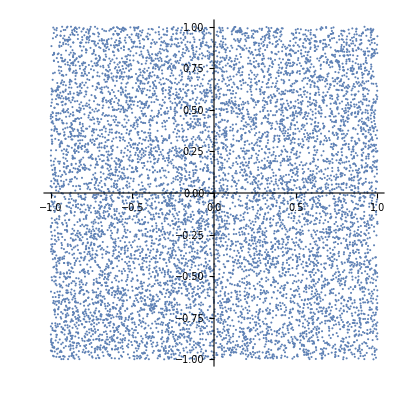

```mathematica
ListPlot[Take[pts,10000],PlotRange->{{-1,1},{-1,1}}, AspectRatio-> 1]
```

Logically, one of the following statements must be true:
1) There are infinitely many points with (x>0, y>0) (Quadrant 1)
2) There are infinitely many points with (x<0, y>0) (Quadrant 2)
3) There are infinitely many points with (x<0, y<0) (Quadrant 3)
4) There are infinitely many points with (x>0, y<0) (Quadrant 4)
5) All quadrants contain finitely many points

Case (5) though contradicts there being an infinite number of points in the sequence! So one of the others must be true.  Since things are symmetrical (“without loss of generality”) let’s assume that (1) is true.  The trick then is to pick some point in the quadrant, color it red, and “zoom in”:

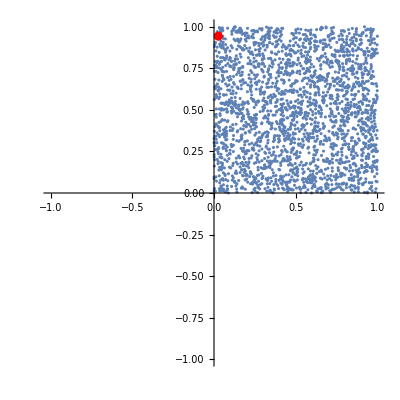

```mathematica
redpoints = {Cases[Take[pts,10000], {x_,y_}/;(x>0)&&(y>0)][[1]]};
Show[ListPlot[Cases[Take[pts,10000], {x_,y_}/;(x>0)&&(y>0)],
PlotRange->{{-1,1},{-1,1}}, AspectRatio-> 1],
ListLinePlot[redpoints, PlotStyle-> Red, PlotMarkers -> Automatic]]
```

Again we ask, one of the following must be true:
1) There are infinitely many points in Quadrant 1 with (x>.5, y>.5) 
2) There are infinitely many points with (x<.5, y>.5)
3) There are infinitely many points with (x<.5, y<.5) 
4) There are infinitely many points with (x>.5, y<.5) 
5) There are finitely many points in Quadrant 1

Since Case (5) contradicts our assumption, we must have one of the other cases.  Again, our illustration for the example is arbitrary, so let’s assume (3) is true.  Then we pick a point to be “red” form this zone, and “zoom” in again

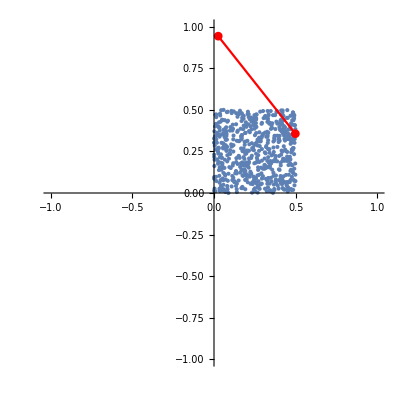

```mathematica
AppendTo[redpoints, Cases[Take[pts,10000], {x_,y_}/;(.5>x>0)&&(.5>y>0)][[2]]];
Show[ListPlot[Cases[Take[pts,10000], {x_,y_}/;(.5>x>0)&&(.5>y>0)],
PlotRange->{{-1,1},{-1,1}}, AspectRatio-> 1],
ListLinePlot[redpoints, PlotStyle-> Red, PlotMarkers -> Automatic]]
```

And so on, find a sub-square that contains infinitely many points, select one of those points, and further restrict our domain.

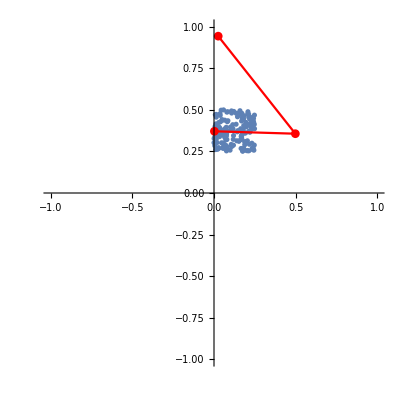

```mathematica
AppendTo[redpoints, Cases[Take[pts,10000], {x_,y_}/;(.25>x>0)&&(.5>y>.25)][[3]]];
Show[ListPlot[Cases[Take[pts,10000], {x_,y_}/;(.25>x>0)&&(.5>y>.25)],
PlotRange->{{-1,1},{-1,1}}, AspectRatio-> 1],
ListLinePlot[redpoints, PlotStyle-> Red, PlotMarkers -> Automatic]]
```

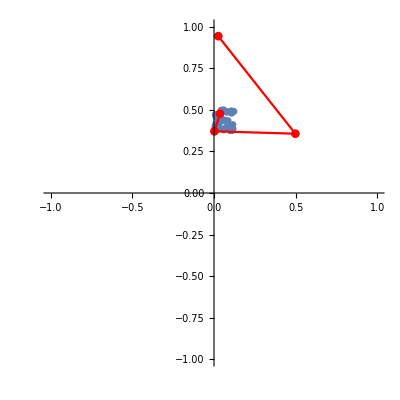

```mathematica
AppendTo[redpoints, Cases[Take[pts,10000], {x_,y_}/;(.125>x>0)&&(.5>y>.375)][[4]]];
Show[ListPlot[Cases[Take[pts,10000], {x_,y_}/;(.125>x>0)&&(.5>y>.375)],
PlotRange->{{-1,1},{-1,1}}, AspectRatio-> 1],
ListLinePlot[redpoints, PlotStyle-> Red, PlotMarkers -> Automatic]]
```

In this way, we can continue to narrow our range and select points such that - if we call our first red point y_1, the second y_2and so on, we will have that:
- All of  y_2, y_3, y_4... are within ϵ = 1 of y_1
- All of   y_3, y_4, y_5... are within ϵ = 1/2 of y_2

- All of y_(n+1), y_(n+2), y_(n+3),...are within ϵ= 1/2^(n-1)of y_n

So - we now we can answer the demand that, given an arbitrarily small ϵ, we find a value n with all points in the subsequence after that point lying within ϵ of the limit point.

## Extensions

While it may seem obscure, the Bolzono-Weirstrass Theorem is at the core of the Intermediate Value Theorem, underlying the theory of calculus, and is essential to the study of compact sets.

## Author contact information

Lauren Berk

lberk@mit.edu

## Guidelines for the Author

### CodeText

### Code